# Physics through Computational Thinking Week-7: Monte Carlo Simulation

Monte Carlo methods are computational algorithms that rely on repeated random sampling to obtain numerical results. In this tutorial, we learn the basics of Monte Carlo simulation using Mathematica.

## 1. Some Necessary Commands

Monte Carlo simulations uses random numbers.

Generating Random Numbers

```mathematica
xmin=-1;
xmax=1;
```

```mathematica
RandomReal[{xmin,xmax}]
```

0.937244

```mathematica
RandomReal[{xmin,xmax},5]
```

{0.348073,0.604262,0.163199,0.59967,-0.658265}

Loops

Two useful methods for doing iterative calculations in Mathematica. 
(i) Do loop : It works well for simple and  nested loops.
(ii) While loop: It is useful for complex loops.

```mathematica
Do[
f = 2x+3;
Print["f=",f],
{x,-1,2,1}
] (*1D loop*)
```

f=1

f=3

f=5

f=7

```mathematica
Do[
f = x*y;
Print["x*y=",f," x=",x," y=",y,"."],
{x,-1,1,1},{y,-1,1,1}
] (*2D loop*)
```

x*y=1 x=-1 y=-1.

x*y=0 x=-1 y=0.

x*y=-1 x=-1 y=1.

x*y=0 x=0 y=-1.

x*y=0 x=0 y=0.

x*y=0 x=0 y=1.

x*y=-1 x=1 y=-1.

x*y=0 x=1 y=0.

x*y=1 x=1 y=1.

```mathematica
x = -0.1; (*initial number*)
cond = Sin[x^2];  (*conditon cond<0.5 *)
While[cond < 0.5,
x = x+0.5;
cond = Sin[x^2];
Print["x=",x];
]
```

x=0.4

x=0.9

```mathematica
Sin[0.9^2]
```

0.724287

In Mathematica, a While loop runs as long as its condition is True. You can include multiple conditions using logical operators: && → AND , || → OR , ! → NOT

```mathematica
i=3; (*initial number*)
While[i<20&&EvenQ[i]==False,
Print[i];
i++;
]
```

3

When one condition is False in intermediate steps, the loop stops immediately.

```mathematica
n=0;
estimate=0;
error=1;
```

```mathematica
While[n<100000&&error>0.001,x=RandomReal[];
estimate=(estimate*n+x^2)/(n+1);
error=Abs[estimate-1/3];
n++;
]
```

```mathematica
{estimate,n}
```

{0.332385,969}

```mathematica
NIntegrate[x^2,{x,0,1}]
```

0.333333

Stop when enough samples are generated OR accuracy is reached. This is a typical Monte Carlo stopping criterion.

RandomReal[] generates x∈[0,1] uniformly. The above example is to find  ∫_0^1 x^2 ⅆx .

```mathematica
nmax=10000;
samples=RandomReal[{0,1},nmax];
values=samples^2;
```

```mathematica
estimate=Accumulate[values]/Range[nmax];
```

```mathematica
(0.05079224590370525+0.3636469637789462+0.24453326007436996)/3
```

0.219657

This calculates ∑_(i=1)^n x_i^2/n  for every n.

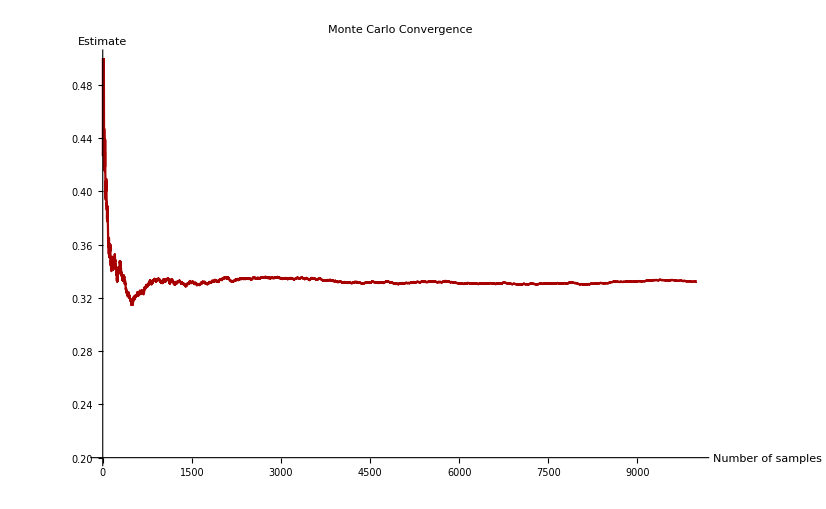

```mathematica
ListLinePlot[estimate,PlotRange->{0.2,0.5},AxesLabel->{"Number of samples","Estimate"},PlotLabel->"Monte Carlo Convergence"]
```

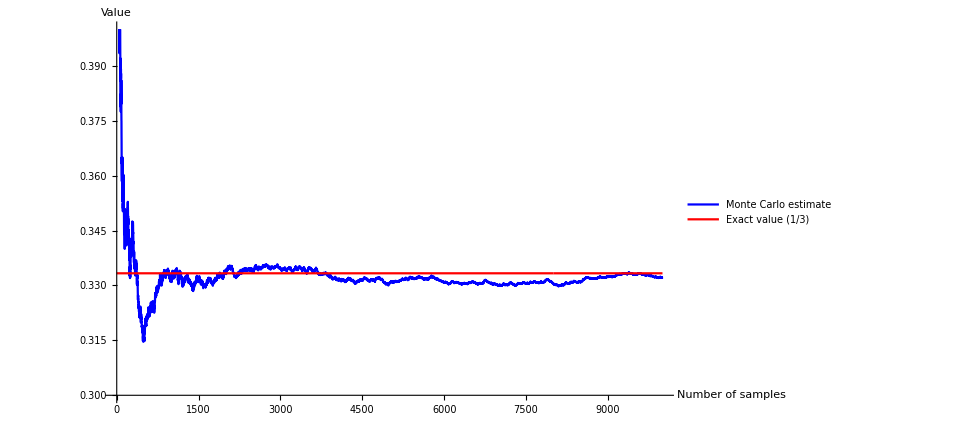

```mathematica
ListLinePlot[{estimate,ConstantArray[1/3,nmax]},PlotStyle->{Blue,Red},PlotRange->{0.3,0.4},PlotLegends->{"Monte Carlo estimate","Exact value (1/3)"},AxesLabel->{"Number of samples","Value"}]
```

The error decreases approximately as  error~1/√N.

```mathematica
Accumulate[{1,2,3}]
```

{1,3,6}

Randomness

In Monte Carlo, we use the mean of random samples to find a value we don’t know.

Example-1: Estimating π by throwing “darts” at a square containing a circle.

```mathematica
n=10000;
points=RandomReal[{-1,1},{n,2}]; (*points lie in the square [−1,1]×[−1,1]*)
insideQ=UnitStep[1-Total[points^2,{2}]]; (*Step 3:Logic test (x^2+y^2<=1)*)
Total[insideQ]; (* count how many darts hit the circle*)
estPi=4.*Total[insideQ]/n
```

3.132

1-(x^2+y^2) -> this quantity tells us whether a point is inside the unit circle.

UniStep[]: step function, it’s returns 1 → point inside the circle, or 0 → point outside the circle.

```mathematica
points1={{0.3,0.4},{0.9,0.7}}
points1^2
Total[points1^2,{2}]
```

{{0.3,0.4},{0.9,0.7}}

{{0.09,0.16},{0.81,0.49}}

{0.25,1.3}

```mathematica
N[π]
```

3.14159

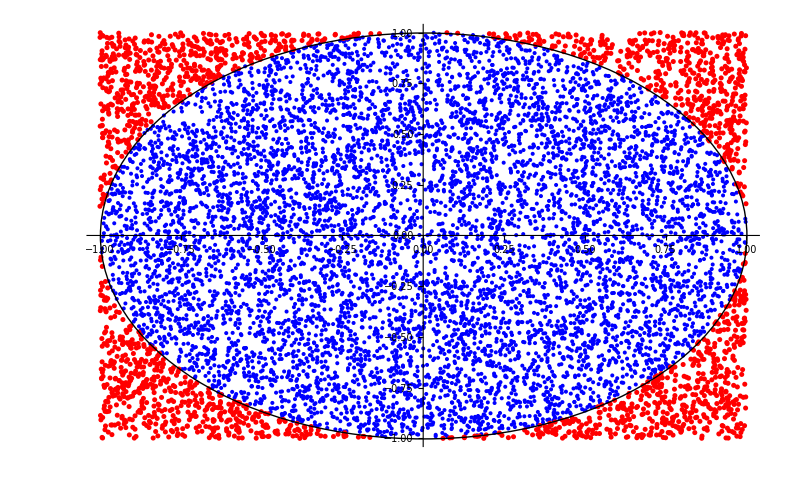

```mathematica
insidePoints=Select[points,#[[1]]^2+#[[2]]^2<=1&];
outsidePoints=Select[points,#[[1]]^2+#[[2]]^2>1&];

Show[ListPlot[insidePoints,PlotStyle->Blue],ListPlot[outsidePoints,PlotStyle->Red],Graphics[{Thick,Circle[{0,0},1]}],PlotRange->{{-1,1},{-1,1}},Axes->True]
```

Blue points → inside circle
Red points → outside circle

```mathematica
Quit[];
```

```mathematica
DynamicModule[{points={},inside=0,total=0,running=False,pts,estPi=0},

Column[{Button[Dynamic[If[running,"Stop","Start"]],running=Not[running]],

Dynamic[
If[running,pts=RandomReal[{-1,1},2];
AppendTo[points,pts];
total++;
If[pts[[1]]^2+pts[[2]]^2<=1,inside++];
estPi=4 *(inside/total);
];

Show[
Graphics[
{PointSize[0.012],LightGray,Rectangle[{-1,-1},{1,1}],Thick,Circle[{0,0},1],
Blue,Point[Select[points,#[[1]]^2+#[[2]]^2<=1&]],
Red,Point[Select[points,#[[1]]^2+#[[2]]^2>1&]]}
],

PlotRange->{{-1,1},{-1,1}},ImageSize->400
],

UpdateInterval->0.03
],

Dynamic@Row[{"Total darts = ",total}],
Dynamic@Row[{"Inside circle = ",inside}],
Dynamic@Row[{"Estimated π = ",N[estPi,6]}]}
]
]
```

```mathematica
N[π]
```

3.14159

The probability of a random point landing in the circle is: P=π/4.

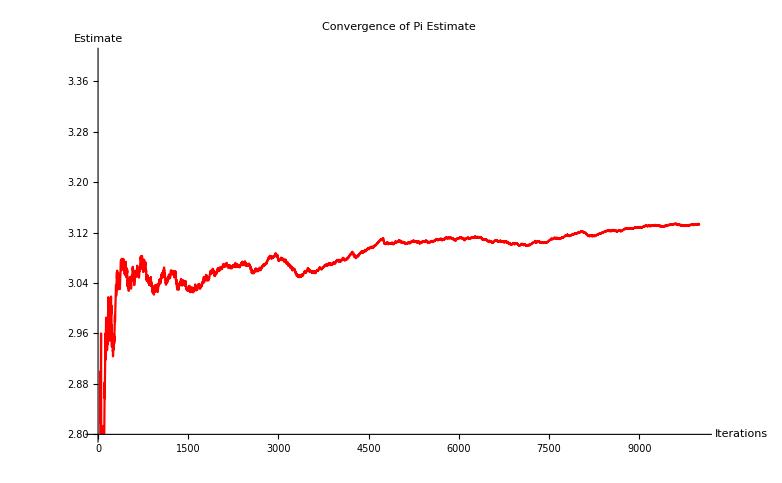

```mathematica
runningMeans=4.0*Accumulate[insideQ]/Range[n];

ListLinePlot[runningMeans,GridLines->{None,{Pi}},PlotStyle->Red,PlotRange->{2.8,3.4},PlotLabel->"Convergence of Pi Estimate",AxesLabel->{"Iterations","Estimate"}]
```

Let’s runs 1000 Monte Carlo experiments, where each experiment throws 500 random darts in the square [−1,1]×[−1,1].

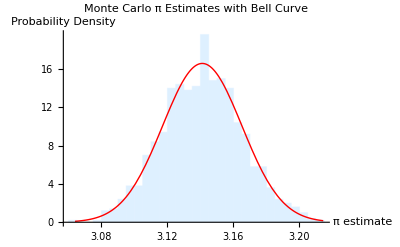

```mathematica
numSimulations=1000;
numDarts=5000;

simulations=Table[
points=RandomReal[{-1,1},{numDarts,2}];
inside=Count[points,p_/;p[[1]]^2+p[[2]]^2<=1];
4.0*inside/numDarts,{numSimulations}];

mean=Mean[simulations];
sigma=StandardDeviation[simulations];

Show[
Histogram[simulations,30,"PDF",PlotLabel->"Monte Carlo π Estimates with Bell Curve",AxesLabel->{"π estimate","Probability Density"},ChartStyle->LightBlue],Plot[PDF[NormalDistribution[mean,sigma],x],{x,Min[simulations],Max[simulations]},PlotStyle->{Red,Thick}]
]
```

Count[list, condition]-> It counts how many elements in list satisfy the condition.

Monte Carlo estimates cluster around the true value (Gaussian-like)

```mathematica
mean=Mean[simulations]
sigma=StandardDeviation[simulations]
```

3.14142

0.0713492

```mathematica
mean=Mean[simulations]
sigma=StandardDeviation[simulations]
```

3.14109

0.024059

Geometric Brownian Motion (GBM) model

In this example, we simulates future stock price paths using Monte Carlo simulation. Let’s assume the stock prices are assumed to follow GBM:

S_T==S_0 exp((μ-σ^2/2)T+σ W_T)

S_T: The simulated price at time T.
S_0: The current (initial) price.
μ: The Drift (expected annual return).
σ: The Volatility (standard deviation of returns).
T: The time horizon (expressed in years).
W_T: Brownian Motion. This is the "random" part. It follows a Normal Distribution with mean 0 and variance T.

```mathematica
S0=100(*Starting Price*);
mu=0.05(*Drift/Expected Return*);
σ=0.2(*Volatility*);
T=1(*Total time:1 year*);
steps=252(*Number of trading days*);
```

```mathematica
pricePath[S0_,mu_,σ_,T_,steps_]:=
S0*Exp[
Accumulate[
RandomVariate[
NormalDistribution[
(mu-σ^2/2)*(T/steps),σ*Sqrt[T/steps]
],
steps]
]
]
```

Each step corresponds to Δt=T/steps. (time increment)  => model evolves daily.
RandomVariate[NormalDistribution[..]] ->​This generates 252 random numbers (steps=252); 
They represent daily log returns.
Accumulate[ ... ] -> computes the cumulative sum of the random returns.

Let’s generate 50 possible future stock trajectories, where each path represents one possible future of the stock.

```mathematica
paths=Table[pricePath[S0,mu,σ,T,steps],{50}];
```

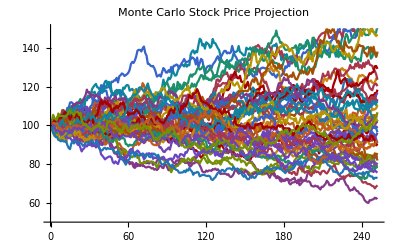

```mathematica
ListLinePlot[paths,PlotRange->{50,150},PlotLabel->"Monte Carlo Stock Price Projection"]
```

Many random curves diverging over time (financial risk). But the average trend follows the drift μ.

Particle Diffusion Simulation

This models how a particle moves randomly in 2D space, similar to Brownian motion.

```mathematica
walk=Accumulate[RandomReal[{-1,1},{1000,2}]]; (*Generate random steps for a particle in 2D space*)
```

Let’s plot the particle path

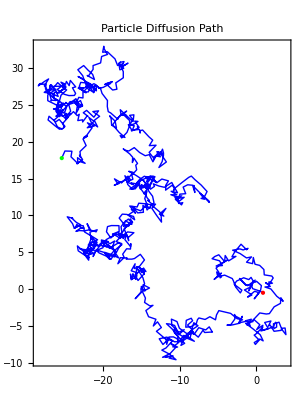

```mathematica
Graphics[{Blue,Line[walk],Red,PointSize[Large],Point[First[walk]],Green,Point[Last[walk]]},
Frame->True,PlotLabel->"Particle Diffusion Path"]
```

🔵 Blue line → path of the particle
🔴 Red point → starting position
🟢 Green point → final position

Monte Carlo simulation for error propagation

Instead of using calculus (derivatives) or the Around object, we performing an experiment 100,000 times to see how the distribution of the result F(x,y) behaves.

```mathematica
Quit[];
```

```mathematica
f[x_,y_]:=x y;
```

```mathematica
samples=Table[f[RandomVariate[NormalDistribution[0.50,0.01]],RandomVariate[NormalDistribution[12.4,0.2]]],{10^5}];
```

6.19954

0.15912

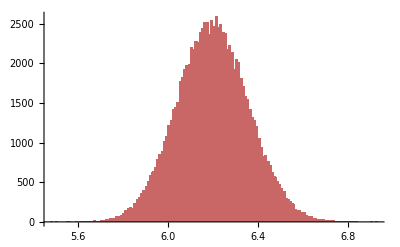

```mathematica
Mean[samples]
StandardDeviation[samples]
Histogram[samples,100]
```

If your function was highly non-linear (e.g., F(x,y) = e^(x/y)), the standard error formula might be slightly wrong ( because Around object uses a linear approximation -- first-order Taylor expansion), while Monte Carlo handles "curved" error spaces perfectly and is exact.

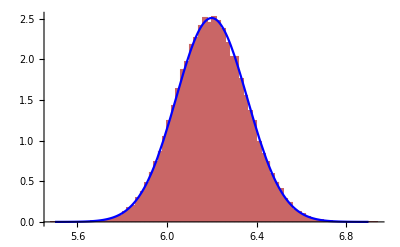

```mathematica
hist=Histogram[samples,50,"PDF"]; (* Comparing to the "Exact" analytic result *)
distPlot=Plot[PDF[NormalDistribution[Mean[samples],StandardDeviation[samples]],x],{x,5.5,6.9},PlotStyle->Blue];

Show[hist,distPlot]
```

Correlated Errors

```mathematica
dist=MultinormalDistribution[{0,0},{{1,0.8},{0.8,1}}];
```

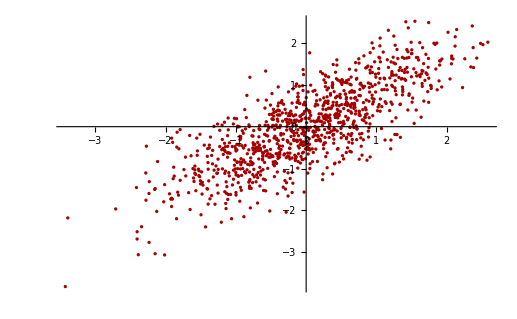

```mathematica
RandomVariate[dist,1000]//ListPlot
```

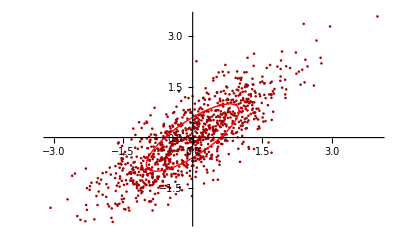

```mathematica
Show[RandomVariate[dist, 1000] // ListPlot, RegionPlot[RegionMember[Ellipsoid[{0, 0}, {{1, 0.8}, {0.8, 1}}], {x, y}], {x, -4, 4}, {y, -4, 4}, PlotStyle -> Transparent, BoundaryStyle -> {Thick, Red}]]
```

```mathematica
cov={{1,0.8},{0.8,1}};  (*Define Covariance Matrix*)
{values,vectors}=Eigensystem[cov];
```

Note: (i) Eigenvectors : direction the ellipse point.
          (ii) Eigenvalues : how long the ellipse is in those directions.

```mathematica
axis1=2*Sqrt[values[[1]]]*vectors[[1]];
axis2=2*Sqrt[values[[2]]]*vectors[[2]];
```

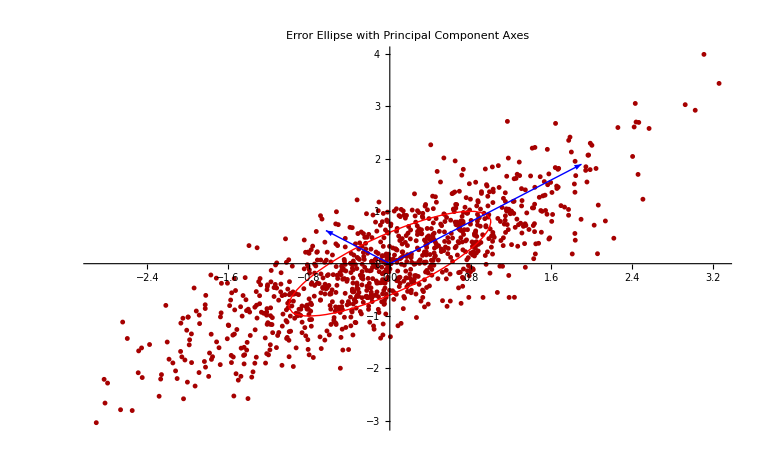

```mathematica
Show[RandomVariate[dist, 1000] // ListPlot, RegionPlot[RegionMember[Ellipsoid[{0, 0}, {{1, 0.8}, {0.8, 1}}], {x, y}], {x, -4, 4}, {y, -4, 4}, PlotStyle -> Transparent, BoundaryStyle -> {Thick, Red}],Graphics[{Thick,Blue,Arrow[{{0,0},axis1}],Arrow[{{0,0},axis2}]}],PlotLabel->"Error Ellipse with Principal Component Axes"
]
```

The Major Axis (Long Arrow): This is the direction of the maximum variance. It represents the primary trend in the data.

The Minor Axis (Short Arrow): This is the direction of minimum variance. It represents the "noise" or the thickness of the correlation.

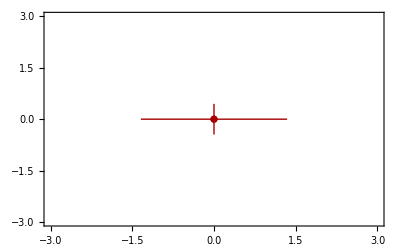

```mathematica
mean={0,0};
covariance={{1,0.8},{0.8,1}};
va=VectorAround[mean,covariance]; (*Using VectorAround for instant visualization*)
ListPlot[{va},PlotRange->{{-3,3},{-3,3}},Frame->True]
```

In Mathematica, the Manipulate command allows us to change the off-diagonal elements of the covariance matrix dynamically.

```mathematica
Manipulate[Module[{cov,vals,vecs,axis1,axis2,dist,pts},
cov={{1,rho},{rho,1}};
{values,vectors}=Eigensystem[cov];
axis1=2*Sqrt[Abs[values[[1]]]]*vectors[[1]];
axis2=2*Sqrt[Abs[values[[2]]]]*vectors[[2]];
SeedRandom[123];dist=MultinormalDistribution[{0,0},cov];
pts=RandomVariate[dist,600];
Show[ListPlot[pts,PlotStyle->Directive[PointSize[Small],Opacity[0.3]],PlotRange->{{-4,4},{-4,4}},Frame->True,AspectRatio->1],RegionPlot[RegionMember[Ellipsoid[{0,0},cov],{x,y}],{x,-4,4},{y,-4,4},PlotStyle->Transparent,BoundaryStyle->{Thick,Red}],Graphics[{Thick,Blue,Arrow[{{0,0},axis1}],Arrow[{{0,0},axis2}]}],PlotLabel->Style["Correlation (ρ) = "<>ToString[rho],14]]],{{rho,0.8,"Correlation (ρ)"},-0.99,0.99,Appearance->"Labeled"}] (*Control:rho ranges from -0.99 to 0.99 to avoid singular matrices*)
```

The "Error" on the fit is essentially the length of that Minor Axis. If the minor axis is very short compared to the major axis, the fit is "good".

Problem-1: Find the integral I=∫_0^1 1/(1+x^4)ⅆx , using the Monte-Carlo method.

```mathematica
Quit[];
```

```mathematica
f[x_]:=1/(1+x^4);

n=10^6;
xs=RandomReal[{0,1},n]; (*Generate random samples b/w [0,1]*)

estInt=Mean[f/@xs]
```

0.866899

Monte Carlo replaces the integral by the average value of the function over random points in the integration region.

∫_a^b f(x)ⅆx≈(b-a)1/N∑_(i=1)^N f(x_i)

```mathematica
NIntegrate[f[x],{x,0,1}]
```

0.866973

Monte Carlo estimate converges nicely.

Problem-2: Draw random numbers from a uniform distribution on [0,1] and keep adding them until their sum exceeds 1. Let ξ be the number of random variables required for the sum to exceed 1. Repeat this experiment 10,000 times, and estimate the mean value of ξ using a Monte Carlo simulation.

```mathematica
trial[a_]:=Module[{sum=0,count=0},
While[sum<=a,
sum+=RandomReal[];
count++;
];
count
]
```

```mathematica
nExp=10000;

results=Table[trial[1],{nExp}]; (*Run simulation*)
est=N[Mean[results]]
```

2.7189

```mathematica
N[ⅇ]
```

2.71828

General results: If you keep adding Uniform(0,1) numbers until the sum exceeds 1 , E[ξ]=e .

Problem-3:

Consider the Jacobian matrix,   A=(a | b
c | d) , where  a,b,c,d∼Normal(0,1) (independent Gaussian random variables).

A saddle point occurs when the determinant is negative: det(A)=ad−bc<0.

Use a Monte Carlo simulation to estimate the fraction of matrices that produce a saddle point.

Simply, we compute the probability P(ad−bc<0) by random sampling .

```mathematica
n=10000;

mats=RandomVariate[NormalDistribution[0,1],{n,4}](*generate random 2*2 matrices in the form {a,b,c,d}*);

dets=mats[[All,1]]*mats[[All,4]]-mats[[All,2]]*mats[[All,3]] ;(*compute determinants*)

fraction=N[Length[Select[dets,#<0&]]/n]
```

0.5067

Let’s change the mean of random variables: a,b,c,d∼Normal(1,1)

```mathematica
n=100000;

mats=RandomVariate[NormalDistribution[1,1],{n,4}](*generate random 2*2 matrices in the form {a,b,c,d}*);

dets=mats[[All,1]]*mats[[All,4]]-mats[[All,2]]*mats[[All,3]] ;(*compute determinants*)

fraction=N[Length[Select[dets,#<0&]]/n]
```

0.50013